## Constants

```mathematica
h = 6.62607015 10^-34;
ℏ = h/(2 π);
μB = 1.4;(*9.274009994 10^-24;*)
μI = 7.62 10^-4;
Efs = h 1.7 10^12;
ahfP2o3 = -7.585  ; 
ahfS = -285.7308  ;
bhfP203 = -3.445 ; 
J=3/2 ;
L = 1;
S = 1/2;
nucspin = 4;
gI = 0.000176490;
gJS = 2.00229421;
```

```mathematica
KroneckerDelta[12,12]
```

1

## Hhf

```mathematica
S=4 ;
IxMatrix =Table[(KroneckerDelta[m,n+1]+KroneckerDelta[m+1,n])*1/2*(S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}]//MatrixForm ;
IzMatrix =-Table[(KroneckerDelta[m,n])*n,{m,-S,S},{n,-S,S}]//MatrixForm ;
IyMatrix =Table[(KroneckerDelta[m,n+1]-KroneckerDelta[m+1,n])*1/(2*I)*(S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}]//MatrixForm ;
```

```mathematica
S=4;
Ix =Table[(KroneckerDelta[m,n+1]+KroneckerDelta[m+1,n])*1/2*(S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Iy=Table[(KroneckerDelta[m,n+1]+KroneckerDelta[m+1,n])*1/(2*I)*(S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Iz=-Table[(KroneckerDelta[m,n])*n,{m,-S,S},{n,-S,S}];
Iplus = Table[KroneckerDelta[m,n+1](S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Iminus =  Table[KroneckerDelta[m+1,n](S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Isq =  Table[KroneckerDelta[m,n](S*(S+1)),{m,-S,S},{n,-S,S}];
```

```mathematica
S=3/2;
Jx =Table[(KroneckerDelta[m,n+1]+KroneckerDelta[m+1,n])*1/2*(S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Jy=Table[(KroneckerDelta[m,n+1]+KroneckerDelta[m+1,n])*1/(2*I)*(S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Jz=-Table[(KroneckerDelta[m,n])*n,{m,-S,S},{n,-S,S}];
Jplus = Table[KroneckerDelta[m,n+1](S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Jminus =  Table[KroneckerDelta[m+1,n](S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Jsq =  Table[KroneckerDelta[m,n](S*(S+1)),{m,-S,S},{n,-S,S}];
```

```mathematica
Sumterm = ahfP2o3*(TensorProduct[Ix,Jx]+TensorProduct[Iy,Jy]+TensorProduct[Iz,Jz]);
```

```mathematica
term2 = μB gJS TensorProduct[IdentityMatrix[9],Jz]+μI*gI*TensorProduct[Iz,IdentityMatrix[4]];
```

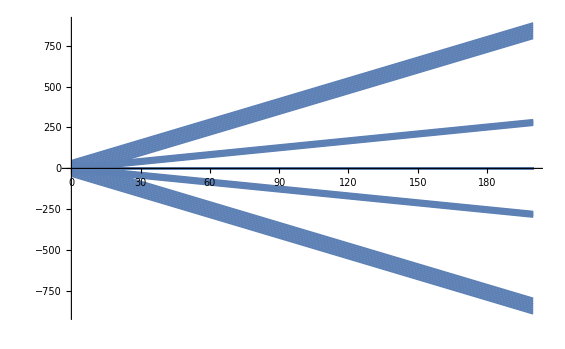

```mathematica
H[B_]:= Sumterm + term2*B 
Plot[H[B],{B,0,200}]
```

```mathematica
Sumterm2 = ahfPS*(TensorProduct[Ix,Jx]+TensorProduct[Iy,Jy]+TensorProduct[Iz,Jz]);
```

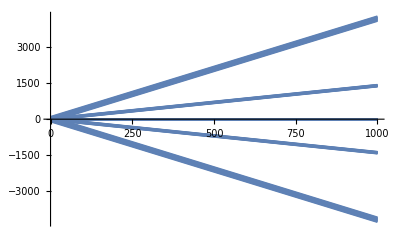

```mathematica
term2 = μB gJS TensorProduct[IdentityMatrix[9],Jz]+μI*gI*TensorProduct[Iz,IdentityMatrix[4]];
H[B_]:= Sumterm 2+ term2*B 
Plot[H[B],{B,0,1000}]
```

```mathematica
Hhf[I_,J_, IJ_]:= ahfP2o3/ℏ^2(IJ) + bhfP203/ℏ^2(3(IJ) - I^2 J^2)/(2I(2I - 1)J(2J -1))
```

```mathematica
F[I_,J_]:= J+I
```

```mathematica
IJ[F_,I_,J_]:=1/2 (F^2-I^2-J^2)
x[B_] := (gJS μB - gI μI)/(ahfS (nucspin+1/2))B
```

## Briet Rabi

```mathematica
Ehf[mF_,B_]:= -ahfS/4+gI μI mF B + (ahfS(nucspin+1/2))/2(1 + (4 mF ((gJS μB - gI μI)/(ahfS (nucspin+1/2))B))/(2nucspin + 1)+((gJS μB - gI μI)/(ahfS (nucspin+1/2))B)^2)^(1/2)
Ehf2[mF_,B_]:=Ehf[mF,10^-4 B]
```

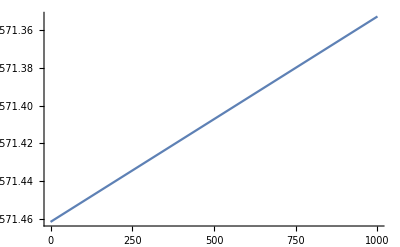

```mathematica
Plot[Ehf2[7/2,B],{B,0,1000},PlotRange->All]
```

```mathematica
Ehf3[F_,mF_,B_]:= -ahfS/4+gI μB mF B + (-1)^(F-1/2)((ahfS 9)/2)/2(1 + (4 mF (((gJS - gI)μB)/(ahfS (nucspin+1/2))B))/(2 9/2)+(((gJS - gI)μB)/(ahfS  9/2)B)^2)^(1/2)
Ehf4[F_,mF_,B_]:=Ehf3[F,mF,10^-4 B]/ℏ
Plot[Ehf4[9/2,Range[-5,4]+1/2,B]/(2π 10^6),{B,0,1000},PlotRange->All]
```

-Graphics-